## Pendulum swing-up, event triggered; horizontal forcing; observe full state (Example 7.12)

```mathematica
Clear["Global`*"];
tff=3; tff1=tff+2; tend=10; clip=100;
```

Calculate feedforward swing-up for 0 < t < τ and balance for τ < t < τ1,  based on nominal model;

```mathematica
SwingupCalc0[tff_,t0_,x0_,xdot0_]:=Module[{eq,bcs,x1,x2,λ1,λ2,x1s,x2s,λ1s,λ2s,us,Es,θdots,t1,t},
t1=t0+tff;  (* final time for feedforward integration *)
eq={
x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]-λ2[t] Cos[x1[t]]^2,
λ1'[t]==Cos[x1[t]]λ2[t](1-Sin[x1[t]]λ2[t]),λ2'[t]==-λ1[t]};
bcs={x1[t0]==x0,x2[t0]==xdot0,x1[t1]==π,x2[t1]==0};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,bcs},{x1,x2,λ1,λ2},{t,t0,t1}];
us=FunctionInterpolation[-λ2s[t]Cos[x1s[t]],{t,t0,t1}];
Es=FunctionInterpolation[1/2 x2s[t]^2+1-Cos[x1s[t]],{t,t0,t1}];
{x1s,x2s,us,Es}  (* Return θ, θ̇, u, E *)];
SwingupCalc[tff_,t0_,tend_,x0_,xdot0_,θold_,θdotold_,uold_,Eold_]:=Module[{θff0,θdotff0,uff0,Eff0,θff,θdotff,uff,Eff,t1},
t1=t0+tff;  (* final time for feedforward integration *)
{θff0,θdotff0,uff0,Eff0}=SwingupCalc0[tff,t0,x0,xdot0];
θff[t_]:=Piecewise[{{θold[t],t<t0},{θff0[t],t0≤t<t1}},π]; (* extend ff to balance *)
θdotff[t_]:=Piecewise[{{θdotold[t],t<t0},{θdotff0[t],t0<t<t1}}]; 
uff[t_]:=Piecewise[{{uold[t],t<t0},{uff0[t],t0≤t<t1}}];
Eff[t_]:=Piecewise[{{Eold[t],t<t0},{Eff0[t],t0≤t<t1}},2];
{θff,θdotff,uff,Eff}]
```

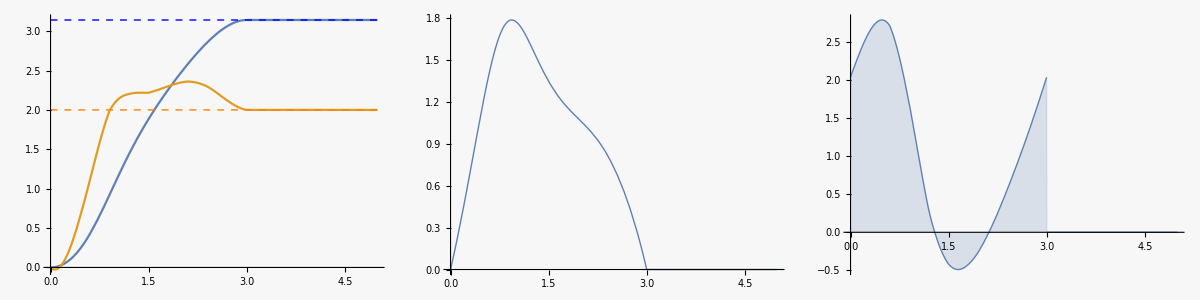

```mathematica
θold[t_]:=0; θdotold[t_]:=0; uold[t_]:=0; Eold[t_]:=0; (* initialize *)
{θff,θdotff,uff,Eff}=SwingupCalc[tff,0,tend,0,0,θold,θdotold,uold,Eold];
pff1=Plot[{θff[t],Eff[t],π,2},{t,0,tff1},PlotStyle->{,,Directive[Blue,Dashed,Thin],Directive[Orange,Dashed,Thin]}, PlotRange->All,ImageSize->200];
pff2=Plot[θdotff[t],{t,0,tff1}, PlotRange->All,ImageSize->200];
pff3=Plot[uff[t],{t,0,tff1},Filling->Axis, PlotRange->All,ImageSize->200];
Grid[{{pff1,pff2,pff3}},Spacings->2]
```

Feedforward & linear feedback, combined

```mathematica
q=({{1, 0}, {0, 1}});   r={{1}};OptimalFeedbackGain[x1_,u1_,q_,r_]:=Module[{a,b,c,sys},
a=({{0, 1}, {-Cos[x1]-u1 Sin[x1], 0}}); b=({{0}, {Cos[x1]}}); c=({{1, 0}});
sys=StateSpaceModel[{a,b,c}];
LQRegulatorGains[sys,{q,r}]  (* optimal feedback gains *)]
```

```mathematica
κ=OptimalFeedbackGain[π,0,q,r][[1]]  (* sign is changed because of hor. forcing *)
```

{-1/(-1+√2),-1/(-1+√2)}

```mathematica
(* Plot[OptimalFeedbackGain[θ,0,q,r][[1]],{θ,0,π},PlotRange->{-5,5}] *)
```

```mathematica
Controller[κ_,t0_,tend_,clip_,θff_,θdotff_,uff_,x0_,xdot0_,td_,d_]:=Module[{eq,init,x1,x2,x1s,x2s,us,Es,κ1,κ2,ufb,u,t},
κ1=κ[[1]]; κ2=κ[[2]];
ufb[t_]:=κ1(θff[t]-x1[t])+κ2 (θdotff[t]-x2[t]);u[t_]:=Clip[uff[t]+ufb[t],{-clip,clip}]; 
eq={x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]+u[t]Cos[x1[t]]};
init={x1[0]==x0,x2[0]==xdot0};  
{x1s,x2s}=NDSolveValue[{eq,init, WhenEvent[t==td,x2[t]-> x2[t]+d]},{x1,x2},{t,t0,tend}]; 
us[t_]:=Clip[uff[t]+κ1(θff[t]-x1s[t])+κ2(θdotff[t]-x2s[t]),{-clip,clip}];
Es[t_]:=1/2 x2s[t]^2+1-Cos[x1s[t]];
{x1s,x2s,us,Es}]
```

InterpolatingFunction::dmval: Input value {3.01613} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.01613} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

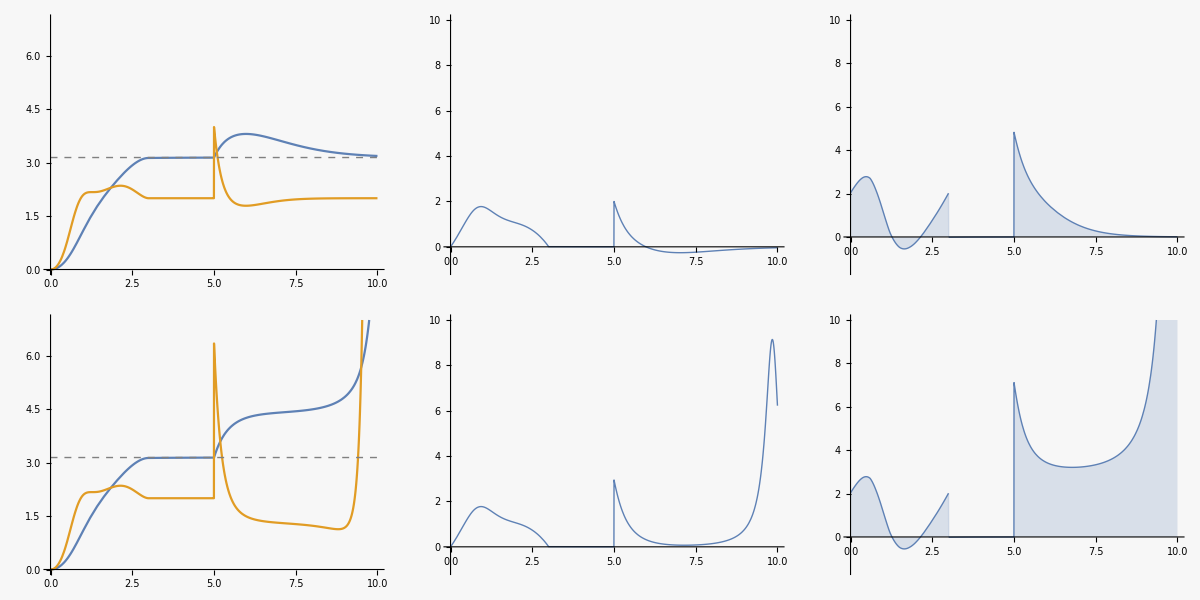

```mathematica
{x1a,x2a,ua,Ea}=Controller[κ,0,tend,clip,θff,θdotff,uff,0,0,tff+2,2];
p1a=Plot[{x1a[t],Ea[t],π},{t,0,tend},PlotStyle->{,,Directive[Gray,Dashed,Thin]}, PlotRange->{0,7},ImageSize->200];
p2a=Plot[x2a[t],{t,0,tend},PlotRange->{-1,10},ImageSize->200];
p3a=Plot[ua[t],{t,0,tend},Filling->Axis,PlotRange->{-1.5,10},ImageSize->200]; 

d0=2.95;
{x1b,x2b,ub,Eb}=Controller[κ,0,tend,clip,θff,θdotff,uff,0,0,tff+2,d0];
p1b=Plot[{x1b[t],Eb[t],π},{t,0,tend},PlotStyle->{,,Directive[Gray,Dashed,Thin]}, PlotRange->{0,7},ImageSize->200];
p2b=Plot[x2b[t],{t,0,tend},PlotRange->{-1,10},ImageSize->200];
p3b=Plot[ub[t],{t,0,tend},Filling->Axis,PlotRange->{-1.5,10},ImageSize->200]; 

Grid[{{p1a,p2a,p3a},{p1b,p2b,p3b}},Spacings->2]
```

Feedforward & linear feedback & event triggering.

Find time t_0 when θ(t_0) = π+1 and extract θ̇(t_0).  Then recalculate the feedforward from t_0.

```mathematica
ControllerEventTriggered0[κ_,tend_,clip_,θff_,θdotff_,uff_,td_,d_]:=Module[{eq,init,x1,x2,x1s,x2s,us,Es,κ1,κ2,ufb,u,t},
κ1=κ[[1]]; κ2=κ[[2]];
ufb[t_]:=κ1(θff[t]-x1[t])+κ2 (θdotff[t]-x2[t]);u[t_]:=Clip[uff[t]+ufb[t],{-clip,clip}];
eq={x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]+u[t]Cos[x1[t]]};
init={x1[0]==x2[0]==0};  
{x1s,x2s}=NDSolveValue[{eq,init, WhenEvent[t==td,x2[t]-> x2[t]+d],WhenEvent[x1[t]==π+1,{Print["pass threshold at ",t,",  θ̇ = ",x2[t]],t0=t,θdot0=x2[t],"StopIntegration"}]},{x1,x2},{t,0,tend}];
us[t_]:=Clip[uff[t]+κ1(θff[t]-x1s[t])+κ2(θdotff[t]-x2s[t]),{-clip,clip}];
Es[t_]:=1/2 x2s[t]^2+1-Cos[x1s[t]];
{x1s,x2s,us,Es}]
```

```mathematica
{x1c,x2c,uc,Ec}=ControllerEventTriggered0[κ,tend,clip,θff,θdotff,uff,tff+2,d0];
```

InterpolatingFunction::dmval: Input value {3.01613} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

pass threshold at 5.71701,  θ̇ = 0.545792

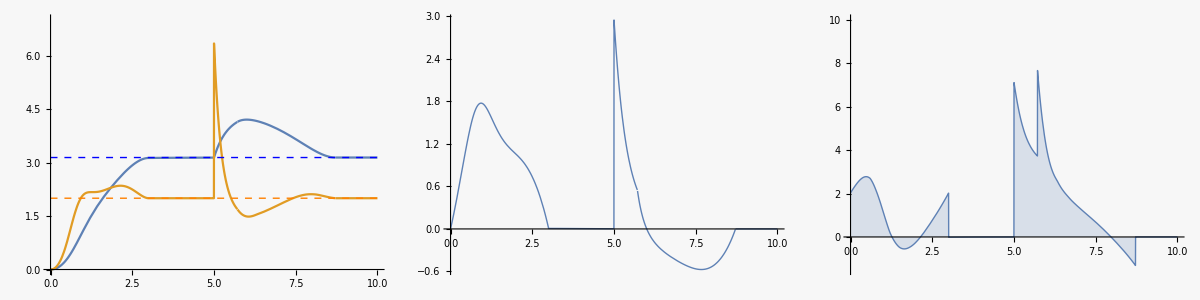

```mathematica
θold=x1c; θdotold=x2c;uold=uc;Eold=Ec; 
{θff,θdotff,uff,Eff}=SwingupCalc[tff,t0,tend,π+1,θdot0,θold,θdotold,uold,Eold];
pff1=Plot[{θff[t],Eff[t],π,2},{t,0,tend},PlotStyle->{,,Directive[Blue,Dashed,Thin],Directive[Orange,Dashed,Thin]}, PlotRange->{0,7},ImageSize->200];
pff2=Plot[θdotff[t],{t,0,tend}, PlotRange->All,ImageSize->200];
pff3=Plot[uff[t],{t,0,tend},Filling->Axis, PlotRange->{-1.5,10},ImageSize->200];
Grid[{{pff1,pff2,pff3}},Spacings->2]
```

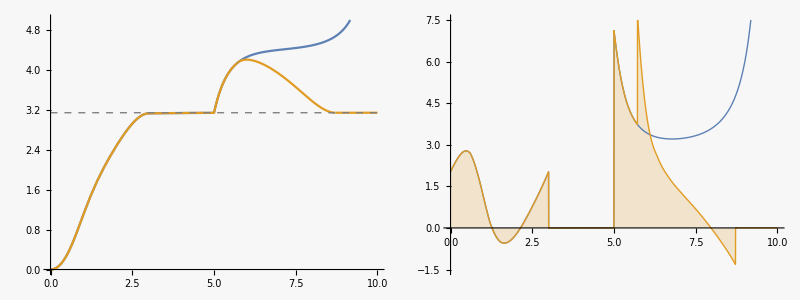

```mathematica
Grid[{{Plot[{x1b[t],θff[t],π},{t,0,tend},PlotStyle->{,,Directive[Gray,Dashed,Thin]}, PlotRange->{0,5},ImageSize->200],
Plot[{ub[t],uff[t]},{t,0,tend},PlotRange->{-1.5,7.5},ImageSize->200,Filling->{2->Axis}]
}},Spacings->4]
```

Export data

```mathematica
dt=0.05;
dat=Table[Through[{x1b,θff,ub,uff}[t]],{t,0,tend,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumEventTrig.dat", dat] 
*)
```